```mathematica
system1={
y'[t]==x[t],
x'[t]==d[t],
(d[t]-5)(d[t]+y[t])==0,
d[0]==k,
x[0]==0,
y[0]==10
};
```

```mathematica
Sol1=NDSolve[
system1/.k->-10,
{y[t],x[t],d[t]},{t,0,100}];
```

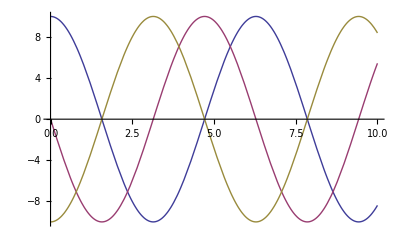

```mathematica
Plot[
{
Evaluate[y[t]/.Sol1],
Evaluate[x[t]/.Sol1],
Evaluate[d[t]/.Sol1]
},
{t,0,10},
PlotRange->All
]
```

```mathematica
Sol2=NDSolve[
system1/.k->5,
{y[t],x[t],d[t]},{t,0,100}];
```

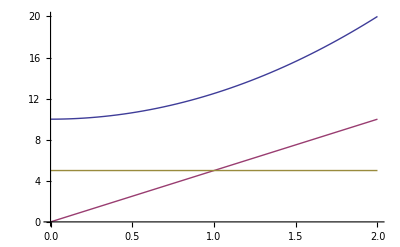

```mathematica
Plot[
{
Evaluate[y[t]/.Sol2],
Evaluate[x[t]/.Sol2],
Evaluate[d[t]/.Sol2]
},
{t,0,2},
PlotRange->All
]
```

Now to try and see how this looks after index reduction:

```mathematica
eq4=D[system1[[3]],t]
```

(d[t]+y[t]) d'[t]+(-5+d[t]) (d'[t]+y'[t])==0

```mathematica
system2eq3Rule=Solve[eq4/.y'[t]->x[t], d'[t]]
```

{{d'[t]→-((-5+d[t]) x[t])/(-5+2 d[t]+y[t])}}

```mathematica
system2eq3=(d'[t]==(d'[t]/.system2eq3Rule)[[1]])
```

d'[t]==-((-5+d[t]) x[t])/(-5+2 d[t]+y[t])

```mathematica
system2={
system1[[1]],system1[[2]],system2eq3,system1[[4]],system1[[5]],system1[[6]]}
```

{y'[t]==x[t],x'[t]==d[t],d'[t]==-((-5+d[t]) x[t])/(-5+2 d[t]+y[t]),d[0]==k,x[0]==0,y[0]==10}

```mathematica
system2/.k->-10
```

{y'[t]==x[t],x'[t]==d[t],d'[t]==-((-5+d[t]) x[t])/(-5+2 d[t]+y[t]),d[0]==-10,x[0]==0,y[0]==10}

```mathematica
Sol3=NDSolve[
system2/.k->-10,
{y[t],x[t],d[t]},{t,0,100}];
```

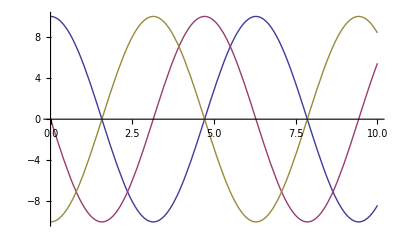

```mathematica
Plot[
{
Evaluate[y[t]/.Sol3],
Evaluate[x[t]/.Sol3],
Evaluate[d[t]/.Sol3]
},
{t,0,10},
PlotRange->All
]
```

```mathematica
Sol4=NDSolve[
system2/.k->5,
{y[t],x[t],d[t]},{t,0,100}]
```

{{y[t]→InterpolatingFunction[{{0.,100.}},<>][t],x[t]→InterpolatingFunction[{{0.,100.}},<>][t],d[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

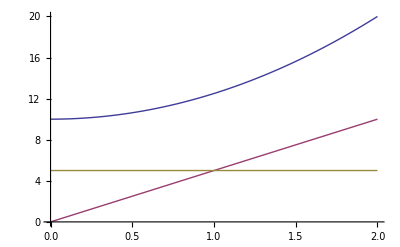

```mathematica
Plot[
{
Evaluate[y[t]/.Sol4],
Evaluate[x[t]/.Sol4],
Evaluate[d[t]/.Sol4]
},
{t,0,2},
PlotRange->All
]
```